1. Renormalization Group Recursive Equations Setup

```mathematica
dim=8;
Clear[μ,η];
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

2. One- and Two-Point Function Setup

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)];
RGΩ:=Block[{},Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

3. One Point Functions: IE and Mag

3.0 Ground State

```mathematica
Clear[μ, IE];
InitRGW;
μ=N[10^9,1000];
kmax=8;
kVector=Range[6,kmax,1];
IE=ConstantArray[0,{Dimensions[kVector][[1]]}];
GSVector=
Do[
kind=1;
InitRGW;
For[i=3,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[IE,kind]=N[1/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT),precN];kind++,];],
{Tx,1,1,1}
];
```

$Aborted

3.1 Internal Energy

```mathematica
Clear[μ,η,IEc]
InitRGW;
(**Temperature for Mag, IE**)
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.005;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv];
(*kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};*)
kVector=Range[6,128,1];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=N[1.0,precN];
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
μ=N[μVector[[μind]],precN];
InitRGW;
For[i=3,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[Part[IE,kind],μind]=N[1/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT),precN];kind++,];],
{Tx,1,Dimensions[μVector][[1]],1}
];
Rasterize[ListLinePlot[Table[Table[{1.0/μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick]]
IEc=IE;
PrependTo[IEc,TVector];
PrependTo[IEc,1.0/μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
IEc=Transpose[IEc];
IEc=PrependTo[IEc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test.csv",IEc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test.csv",IEc](*For Windows*)*)
```

-Graphics-

3.2 Magnetization vs H (big)

```mathematica
(*μ=4.85165*10^8;T=0.1;
μ=22026.5;       T=0.2;
μ=54.5982;       T=0.5;
μ=7.38906;       T=1.0;
μ=3.0;           T=1.82048;
μ=2.71828;       T=2.0;
μ=1.49182;       T=5;
μ=1.2214;        T=10;
μ=1.0;           T=10^9; 
*)
```

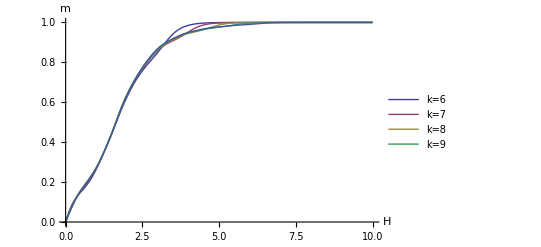

```mathematica
(* μ=7.389; T=1.0 *)
Clear[μ,η,MagHc]
InitRGW;
precN=1000;
kVector=Range[6,10,1];
InitRGW;
μ=N[7.389,100];(*1:high T;1000:low T*)
Hmin=0;
Hmax=10;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=N[Exp[-Hmin],precN];
ηmin=N[Exp[-Hmax],precN];
ηVector=N[Exp[-HVector],precN];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H*)
InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=N[ηVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=N[1/(2^(j+1)+1)*(dA0dη.Υ).(DLnZ1/.SAT),precN];kind++,];
];
];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m7d389_test.csv",MagHc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m7d389_test.csv",MagHc](*For Windows*)*)
```

3.3 Magnetization vs H (small)

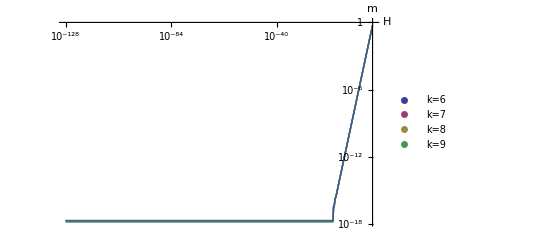

```mathematica
(*μ=3*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=Range[1,0.1,-0.025];
HVector=Join[HVector,Range[0.1-0.0025,0.01,-0.0025]];
HVector=Join[HVector,Range[0.01-0.00025,0.001+0.00025,-0.00025]];
HVector=Join[HVector,10^Range[-3,-64,-0.25]];
HVector=Join[HVector,10^Range[-64.5,-128,-0.5]];
HVecotr=N[HVector,precN];
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,10,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
μ=3;
kind=1;
Clear[η];
InitRGW;
η=N[ηVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=N[1/(2^(j+1)+1)*(dA0dη.Υ).(DLnZ1/.SAT),precN];
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{"H","m"}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,15]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m3_test.csv",MagHc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m3_test.csv,MagHc](*For Windows*)*)
```

3.4 Magnetization vs μ 
<m> vs μ at different H

H=0.01; η=0.9900498337

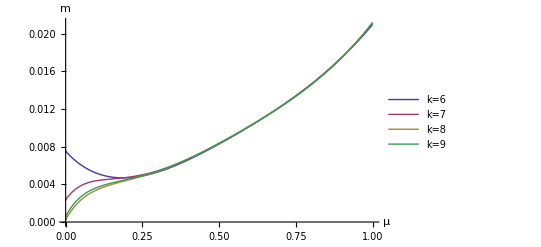

```mathematica
(*H=1e-2*)
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
H=1/10^2;
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.005;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv];
kVector=Range[6,128,1];
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6],"; η=",N[η,10]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[Magμ,kind],i]=N[1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),20];++kind,];];];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μinvVector,15]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_magm_H1e-2_test.csv",Magμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magm_H1e-2_test.csv,Magμc](*For Windows*)*)
```

4. Two Point Functions : Cv and χ

4.1 Specific Heat Cv

0.09625 Completed.

0.1925 Completed.

0.2887 Completed.

0.385 Completed.

0.4812 Completed.

0.5775 Completed.

0.6737 Completed.

0.77 Completed.

0.8662 Completed.

0.9625 Completed.

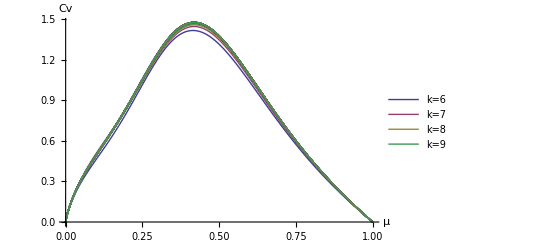

```mathematica
Clear[η,μ,Cvμc]
precN=1000;
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=N[1.0, precN];
(**Temperature for Cv, X**)
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
kVector=Range[6,64,1];
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(*Magnetization at different H at μ=0.01*);
μind=0;
Do[
kind=1;
μind++;
(*Save results in the middle*)
If[Mod[μind,100]==0,Print[N[μind/Dimensions[μVector][[1]],4]," Completed."];
Clear[Cvμc,kVectorc];
kVectorc=kVector;
Cvμc=Cvμ;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_pre.csv",Cvμc];
];
(*Save results in the middle*)
Clear[μ];
InitRGΩ;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=N[DLnZ1/.SAT,precN];
DDlnZ=N[D2LnZ1/.SAT,precN];
term0=N[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ,precN];
term1=N[d2μdβ2*(dA0dμ.Υ).DlnZ,precN];
term2=N[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ),precN];
term3=N[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ),precN];
Part[Part[Cvμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/TVector[[μind]],precN];
kind++,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
Cvμc=Cvμ;
kVectorc=kVector;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_pre.csv",Cvμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_test.csv,Cvμc](*For Windows*)*)
```

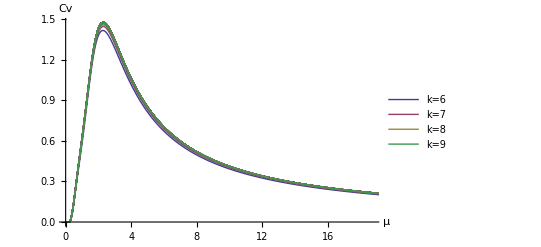

```mathematica
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
ListLinePlot[Table[Table[{TVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
```

4.2 Susceptibility χ

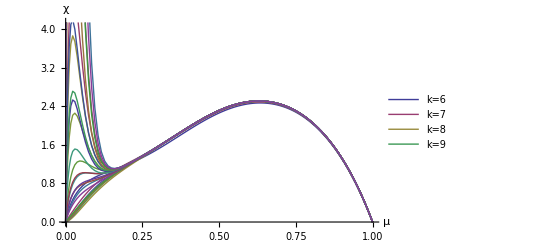

```mathematica
(************************* χ at H=0 ****************************)
Clear[η,μ,χμ,χμc]
H=0;
kVector=Range[6,32,1];
precN=500;
Tmin=0.01;
Tmax=10.01;
Tinc=0.04;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dηdH)^2*(d2A0dη2.Υ).DlnZ,precN];
term1=N[d2ηdH2*(dA0dη.Υ).DlnZ,precN];
term2=N[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη),precN];
term3=N[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ),precN];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/μVector[[μind]]*4.0/TVector[[μind]],20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_pre_k632_the.csv",χμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_X_test.csv,χμc](*For Windows*)*)
```

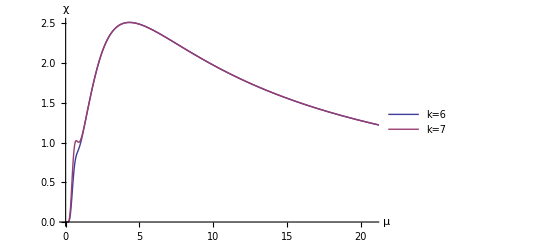

```mathematica
ListLinePlot[Table[Table[{TVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,14,15}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
```

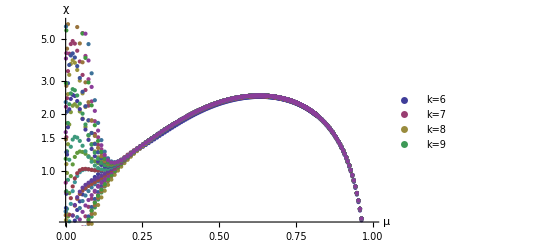

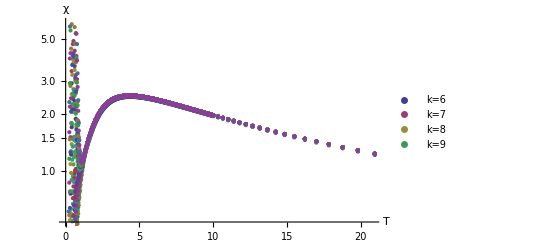

```mathematica
ListLogPlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
ListLogPlot[Table[Table[{TVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"T","χ"}]
```

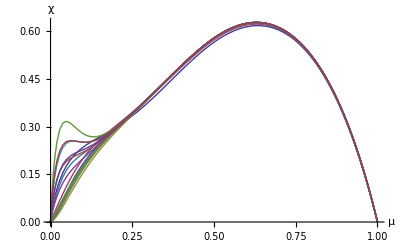

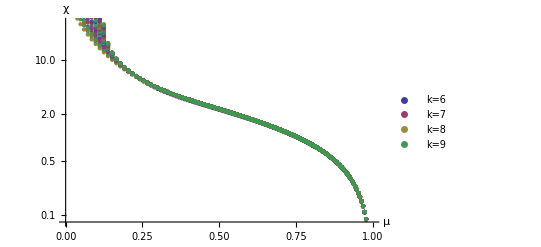

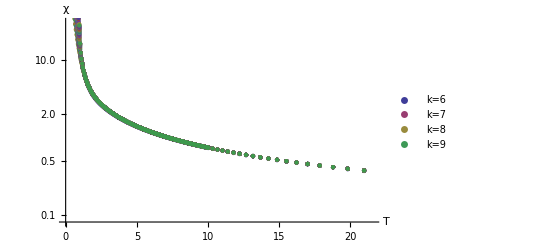

```mathematica
(************************* χ at H=10^(-4) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-4);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-4.csv",χμc];
```

-Graphics-

```mathematica
(************************* χ at H=10^(-8) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-8);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-8.csv",χμc];
```

-Graphics-

```mathematica
(************************* χ at H=10^(-16) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-16);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-16.csv",χμc];
```

-Graphics-